## Free Spectral Densities

## Clear Everything

```mathematica
ClearAll["Global`*"];
```

## Define Functions

```mathematica
(* Number of basis states *)
numStates[npart_,Δmax_]:=Which[Δmax<(3/2)*npart,0,npart==1,1,npart≠ 1,ToExpression["counts"<>ToString[npart]][[1;;Floor[Δmax-(3/2)npart+1]]]//Total];
```

```mathematica
(* Kinetic function *)
kineticFunc[npart_,Δmax_,kmax_,ratioWidth_]:=Module[{size=numStates[npart,Δmax],μsq},
If[npart==1,{0.},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]];
KroneckerProduct[IdentityMatrix[size],DiagonalMatrix[Table[(μsq[[k]]+μsq[[k+1]])/2,{k,kmax}]]]//N]];
```

```mathematica
(* Mass function *)
massFunc[npart_,Δmax_,kmax_]:=Module[{size=numStates[npart,Δmax]},
If[npart==1,{1.},
KroneckerProduct[Chop[ToExpression["BasisMass"<>ToString[npart]][[1;;size,1;;size]],10^-35],IdentityMatrix[kmax]]]];
```

```mathematica
(* Compute eigenvalues and eigenvecs *)
eigensys[mat_]:=Eigensystem[mat]//Transpose//Sort//Transpose;
eigenvals[mat_]:=Eigenvalues[mat]//Sort;
minVal[mat_]:=Eigenvalues[mat]//Min;
minvals[nVals_,mat_]:=eigenvals[mat][[1;;nVals]];
```

```mathematica
(* Useful coefficient *)
𝒜[M_,k_,kp_]:=𝒜[M,k,kp]= 
Module[{n,Km,Kp,perms,multiplicity,parts,qvecs},
n=Length[k];
perms=Permutations[kp];
multiplicity=Times@@(Tally[kp][[All,2]]!);

multiplicity*
Sum[
Km=k[[All,1]]+kpp[[All,1]];
Kp=k[[All,2]]+kpp[[All,2]];
parts=IntegerPartitions[M,n];parts=PadRight[parts,{Length[parts],n}];
parts=Flatten[Permutations[#]&/@parts,1];
qvecs=Select[parts,Min[Kp/2-#]≥0&];
Sum[Times@@(Binomial[Kp,2q]Pochhammer[1/2,q]Pochhammer[1/2,Km]Pochhammer[Km+1/2,Kp-q]),{q,qvecs}]
,{kpp,perms}]//Simplify];

(* Monomial inner product (exact) *)
InnerFT[k_,kp_]:=Module[{n=Length[k],TotDeriv,TotPerp},
TotDeriv=Total[k,2]+Total[kp,2];
TotPerp=Total[k[[All,2]]]+Total[kp[[All,2]]];
If[OddQ[TotPerp],0,
π^2/((4π)^n 2^(n-4)Gamma[(TotPerp+n-1)/2])Sum[((-1)^(TotPerp/2-M)Gamma[TotPerp/2-M+1/2])/Gamma[TotDeriv-M+n/2] 𝒜[M,k,kp],{M,0,TotPerp/2}]//Simplify]
];
```

```mathematica
(* μOverlaps is missing an overall factor of P^Vminus Λ^(Vperp+(n-1)/2). Need to put this in by hand when computing spectral densities. *)
μOverlaps[n_,kmax_,Vperp_,ratioWidth_]:=Module[{μsq},
μsq=Accumulate[Prepend[Table[ratioWidth^(kmax-k),{k,kmax}]/Sum[ratioWidth^(kmax-k),{k,kmax}],0]]//N;
1/(√(2π))1/((n+1+2Vperp)/4)Table[(μsq[[k+1]]^((n+1+2Vperp)/4)-μsq[[k]]^((n+1+2Vperp)/4))/(√(μsq[[k+1]]-μsq[[k]])),{k,kmax}]]
```

```mathematica
ϕnOverlapFunc[npart_,Δmax_,kmax_,ratioWidth_]:=Module[{size=numStates[npart,Δmax],mons,basis,monOverlaps,basisOverlaps},
mons=ToExpression["mons"<>ToString[npart]][[1;;size]];
basis=ToExpression["basis"<>ToString[npart]][[1;;size,1;;size]];
monOverlaps=InnerFT[ConstantArray[{0,0},npart],#]&/@mons;
basisOverlaps=basis.monOverlaps;
KroneckerProduct[basisOverlaps,μOverlaps[npart,kmax,0,ratioWidth]]//Flatten
];
```

## ϕ^n Spectral Density

### ϕ^2

```mathematica
DMAX=16;
npart=2;
```

```mathematica
(* Load data *)
dir="/Users/matt/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";*)
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas"<>ToString[npart]<>"Mass"];
```

```mathematica
dmax=16;
kmax=65;
ratioWidth=8/10;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)))
```

1411.16

```mathematica
t1=AbsoluteTime[];

kinetic=kineticFunc[npart,dmax,kmax,ratioWidth];
mass=massFunc[npart,dmax,kmax];
ϕnOverlaps=ϕnOverlapFunc[npart,dmax,kmax,ratioWidth];

{vals,vecs}=eigensys[Λ^2*kinetic+m^2*mass];
ϕnIntegratedSpec=Thread[{√vals,Λ^(npart-1)*Accumulate[(vecs.ϕnOverlaps)^2]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.00130573

```mathematica
Specϕ2D16=ϕnIntegratedSpec;
```

```mathematica
SpecThy[n_,μ_]:=n/(4π)^(n-1)(μ-n*m)^(n-1)

thytable=Table[SpecThy[npart,μ],{μ,√vals}];
ratio2=Thread[{Specϕ2D16[[All,1]],Specϕ2D16[[All,2]]/thytable}];
```

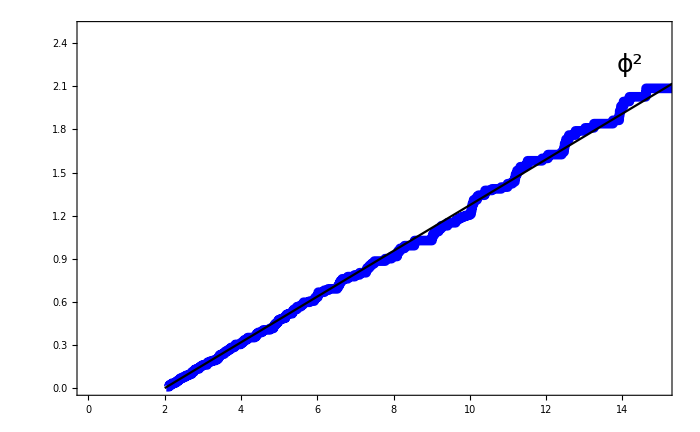

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset2=Show[ListPlot[ratio2,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,10},{0.7,1.3}}],line];

temp2=ListLinePlot[Specϕ2D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,15},{0,2.5}},LabelStyle->Black,Epilog->{Inset[inset2,{1.8,2.6},{.5,1.5},6.5],Inset[Style["ϕ^2",FontFamily->"Times",FontSize->25],{14.2,2.25},{0,0},FormatType->TraditionalForm,BaseStyle->20],(*Inset[Style["Δ_max = 16\n i_max = 50\n Λ_IR = 0.5",FontFamily->"Times"],{8.5,.3},{0,0},FormatType->TraditionalForm,BaseStyle->16]*)}];
thy2=Plot[SpecThy[2,μ],{μ,2m,50},PlotStyle->{Black}];
plot2=Show[temp2,thy2]
```

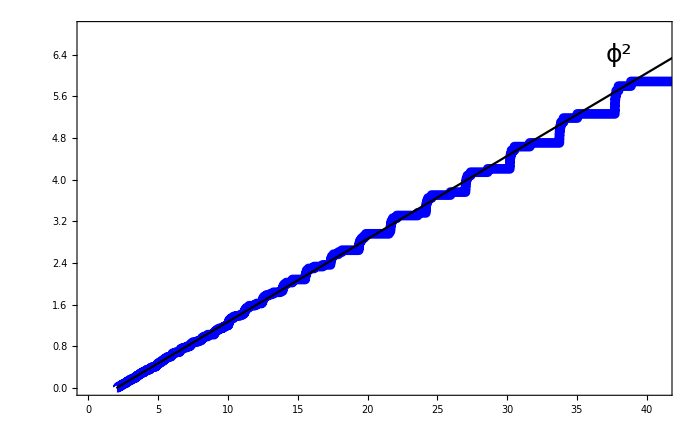

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset2=Show[ListPlot[ratio2,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp2=ListLinePlot[Specϕ2D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.002]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,41},{0,6.9}},LabelStyle->Black,Epilog->{Inset[inset2,{4.2,1.06*6.9},{.5,1.5},19.],Inset[Style["ϕ^2",FontFamily->"Times",FontSize->25],{38,6.4},{0,0},FormatType->TraditionalForm,BaseStyle->20](*Inset[Style["Δ_max = 16\n i_max = 50\n Λ_IR = 0.5",FontFamily->"Times"],{8.5,.3},{0,0},FormatType->TraditionalForm,BaseStyle->16]*)}];
thy2=Plot[SpecThy[2,μ],{μ,2m,100},PlotStyle->{Black}];
plot2ZoomOut=Show[temp2,thy2]
```

```mathematica
(* plot=ListPlot[Specϕ2D16,Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->14,ImageSize->500,PlotRange->{{0,10},{0,1.5}},Joined->True,PlotMarkers->{Style["●"],3},PlotStyle->{{Blue,Thickness[.003]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=16","",""},LabelStyle->{FontFamily->"Times",14},LegendLayout->{"Row",5}],{.9,.15}]];
thy2=Plot[SpecThy[2],{μ,2m,50},PlotStyle->{Black}];
Show[plot,thy2] *)
```

### ϕ^3

```mathematica
DMAX=16;
npart=3;
```

```mathematica
(* Load data *)
dir="/Users/matt/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";*)
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas"<>ToString[npart]<>"Mass"];
```

```mathematica
dmax=16;
kmax=65;
ratioWidth=8/10;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)))
```

1411.16

```mathematica
t1=AbsoluteTime[];

kinetic=kineticFunc[npart,dmax,kmax,ratioWidth];
mass=massFunc[npart,dmax,kmax];
ϕnOverlaps=ϕnOverlapFunc[npart,dmax,kmax,ratioWidth];

{vals,vecs}=eigensys[Λ^2*kinetic+m^2*mass];
ϕnIntegratedSpec=Thread[{√vals,Λ^(npart-1)*Accumulate[(vecs.ϕnOverlaps)^2]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.525974

```mathematica
Specϕ3D16=ϕnIntegratedSpec;
```

```mathematica
SpecThy[n_,μ_]:=n/(4π)^(n-1)(μ-n*m)^(n-1)

thytable=Table[SpecThy[npart,μ],{μ,√vals}];
ratio3=Thread[{Specϕ3D16[[All,1]],Specϕ3D16[[All,2]]/thytable}];
```

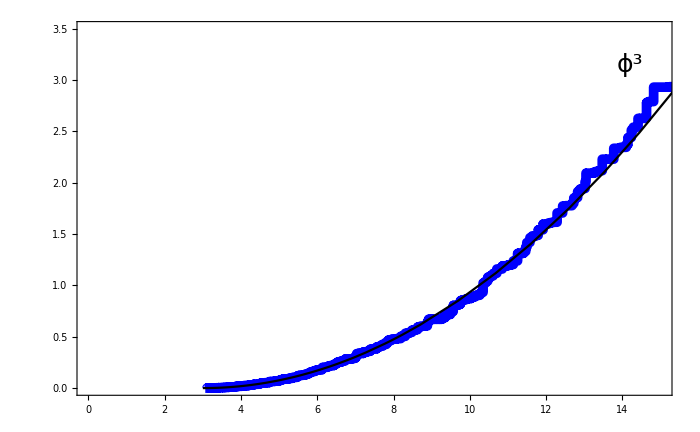

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset3=Show[ListPlot[ratio3,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp3=ListLinePlot[Specϕ3D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,15},{0,3.5}},LabelStyle->Black,Epilog->{Inset[inset3,{1.8,3.65},{.5,1.5},6.5],Inset[Style["ϕ^3",FontFamily->"Times",FontSize->25],{14.2,3.15},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy3=Plot[SpecThy[3,μ],{μ,npart*m,50},PlotStyle->{Black}];
plot3=Show[temp3,thy3]
```

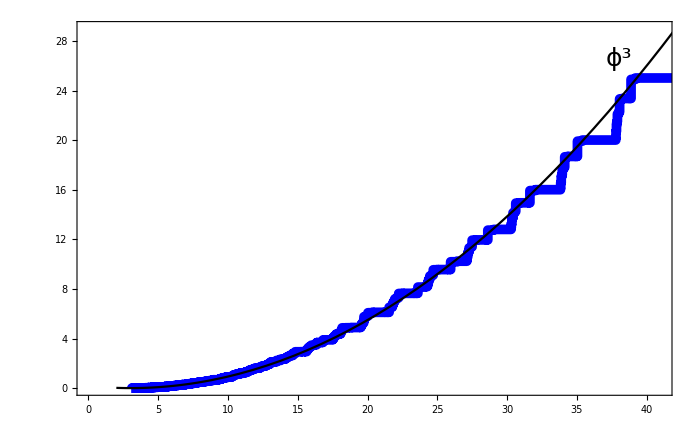

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset3=Show[ListPlot[ratio3,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp3=ListLinePlot[Specϕ3D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.002]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,41},{0,29}},LabelStyle->Black,Epilog->{Inset[inset3,{4.2,1.06*29},{.5,1.5},19],Inset[Style["ϕ^3",FontFamily->"Times",FontSize->25],{38,26.6},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy3=Plot[SpecThy[3,μ],{μ,npart*m,50},PlotStyle->{Black}];
plot3ZoomOut=Show[temp3,thy3]
```

```mathematica
(* plot=ListPlot[Specϕ2D16,Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->14,ImageSize->500,PlotRange->{{0,10},{0,1.5}},Joined->True,PlotMarkers->{Style["●"],3},PlotStyle->{{Blue,Thickness[.003]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=16","",""},LabelStyle->{FontFamily->"Times",14},LegendLayout->{"Row",5}],{.9,.15}]];
thy2=Plot[SpecThy[2],{μ,2m,50},PlotStyle->{Black}];
Show[plot,thy2] *)
```

### ϕ^4

```mathematica
DMAX=16;
npart=4;
```

```mathematica
(* Load data *)
dir="/Users/matt/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";*)
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas"<>ToString[npart]<>"Mass"];
```

```mathematica
dmax=16;
kmax=65;
ratioWidth=8/10;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)))
```

1411.16

```mathematica
t1=AbsoluteTime[];

kinetic=kineticFunc[npart,dmax,kmax,ratioWidth];
mass=massFunc[npart,dmax,kmax];
ϕnOverlaps=ϕnOverlapFunc[npart,dmax,kmax,ratioWidth];

{vals,vecs}=eigensys[Λ^2*kinetic+m^2*mass];
ϕnIntegratedSpec=Thread[{√vals,Λ^(npart-1)*Accumulate[(vecs.ϕnOverlaps)^2]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 5.62465

```mathematica
Specϕ4D16=ϕnIntegratedSpec;
```

```mathematica
SpecThy[n_,μ_]:=n/(4π)^(n-1)(μ-n*m)^(n-1)

thytable=Table[SpecThy[4,μ],{μ,√vals}];
ratio4=Thread[{Specϕ4D16[[All,1]],Specϕ4D16[[All,2]]/thytable}];
```

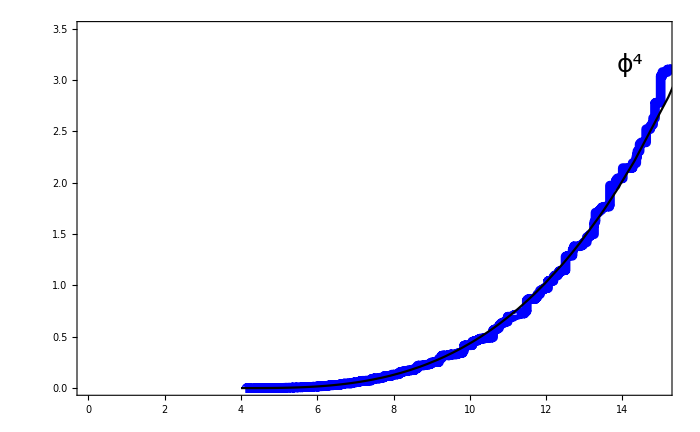

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset4=Show[ListPlot[ratio4,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,20},{0.7,1.3}}],line];

temp4=ListLinePlot[Specϕ4D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,15},{0,3.5}},LabelStyle->Black,Epilog->{Inset[inset4,{1.8,3.65},{.5,1.5},6.5],Inset[Style["ϕ^4",FontFamily->"Times",FontSize->25],{14.2,3.15},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy4=Plot[SpecThy[4,μ],{μ,4*m,50},PlotStyle->{Black}];
plot4=Show[temp4,thy4]
```

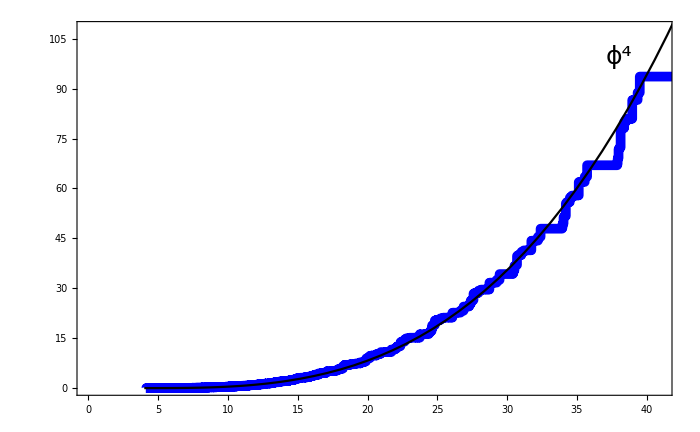

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset4=Show[ListPlot[ratio4,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp4=ListLinePlot[Specϕ4D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.002]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,41},{0,108}},LabelStyle->Black,Epilog->{Inset[inset4,{4.2,1.06*108},{.5,1.5},19],Inset[Style["ϕ^4",FontFamily->"Times",FontSize->25],{38,99.5},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy4=Plot[SpecThy[4,μ],{μ,4*m,50},PlotStyle->{Black}];
plot4ZoomOut=Show[temp4,thy4]
```

```mathematica
(* plot=ListPlot[Specϕ2D16,Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->14,ImageSize->500,PlotRange->{{0,10},{0,1.5}},Joined->True,PlotMarkers->{Style["●"],3},PlotStyle->{{Blue,Thickness[.003]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=16","",""},LabelStyle->{FontFamily->"Times",14},LegendLayout->{"Row",5}],{.9,.15}]];
thy2=Plot[SpecThy[2],{μ,2m,50},PlotStyle->{Black}];
Show[plot,thy2] *)
```

### ϕ^5

```mathematica
DMAX=16;
npart=5;
```

```mathematica
(* Load data *)
dir="/Users/matt/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
(*dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";*)
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas"<>ToString[npart]<>"Mass"];
```

```mathematica
dmax=16;
kmax=65;
ratioWidth=8/10;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)))
```

1411.16

```mathematica
t1=AbsoluteTime[];

kinetic=kineticFunc[npart,dmax,kmax,ratioWidth];
mass=massFunc[npart,dmax,kmax];
ϕnOverlaps=ϕnOverlapFunc[npart,dmax,kmax,ratioWidth];

{vals,vecs}=eigensys[Λ^2*kinetic+m^2*mass];
ϕnIntegratedSpec=Thread[{√vals,Λ^(npart-1)*Accumulate[(vecs.ϕnOverlaps)^2]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 1.23256

```mathematica
Specϕ5D16=ϕnIntegratedSpec;
```

```mathematica
SpecThy[n_,μ_]:=n/(4π)^(n-1)(μ-n*m)^(n-1)

thytable=Table[SpecThy[5,μ],{μ,√vals}];
ratio5=Thread[{Specϕ5D16[[All,1]],Specϕ5D16[[All,2]]/thytable}];
```

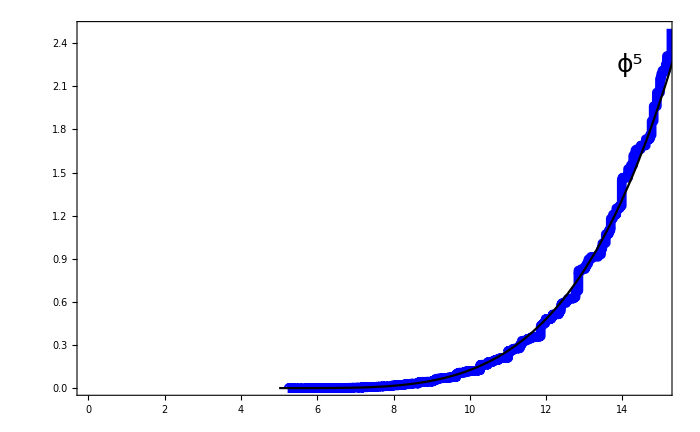

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset5=Show[ListPlot[ratio5,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp5=ListLinePlot[Specϕ5D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.005]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,15},{0,2.5}},LabelStyle->Black,Epilog->{Inset[inset5,{1.8,2.6},{.5,1.5},6.5],Inset[Style["ϕ^5",FontFamily->"Times",FontSize->25],{14.2,2.25},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy5=Plot[SpecThy[5,μ],{μ,5*m,50},PlotStyle->{Black}];
plot5=Show[temp5,thy5]
```

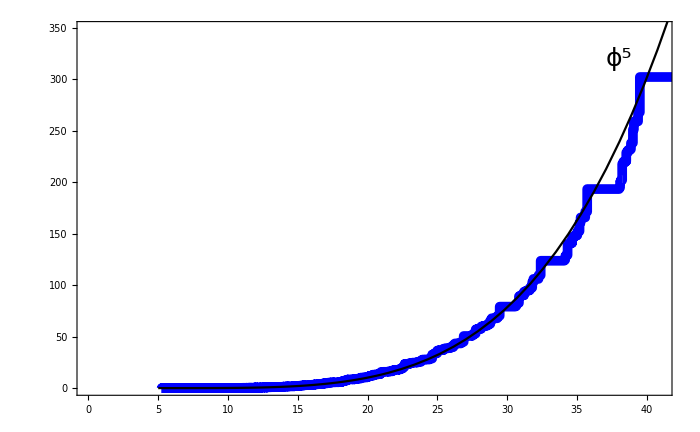

```mathematica
line=Plot[1,{x,0,50},PlotStyle->{Black}];
inset5=Show[ListPlot[ratio5,Frame->True,FrameStyle->Thickness[0.003],FrameTicksStyle->12,ImageSize->700,LabelStyle->Black,PlotStyle->{Blue,PointSize[0.02]},PlotRange->{{0,15},{0.7,1.3}}],line];

temp5=ListLinePlot[Specϕ5D16,Frame->True,FrameStyle->Directive[{Black,Thickness[0.002]}],FrameTicksStyle->16,ImageSize->700,PlotStyle->{{Blue,Thickness[.01]}},InterpolationOrder->0,PlotRange->{{0,41},{0,349}},LabelStyle->Black,Epilog->{Inset[inset5,{4.2,1.06*349},{.5,1.5},19],Inset[Style["ϕ^5",FontFamily->"Times",FontSize->25],{38,320},{0,0},FormatType->TraditionalForm,BaseStyle->20]}];
thy5=Plot[SpecThy[5,μ],{μ,5*m,50},PlotStyle->{Black}];
plot5ZoomOut=Show[temp5,thy5]
```

```mathematica
(* plot=ListPlot[Specϕ2D16,Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->14,ImageSize->500,PlotRange->{{0,10},{0,1.5}},Joined->True,PlotMarkers->{Style["●"],3},PlotStyle->{{Blue,Thickness[.003]}},PlotLegends->Placed[SwatchLegend[{"Δ_max=16","",""},LabelStyle->{FontFamily->"Times",14},LegendLayout->{"Row",5}],{.9,.15}]];
thy2=Plot[SpecThy[2],{μ,2m,50},PlotStyle->{Black}];
Show[plot,thy2] *)
```

### Grid Plot

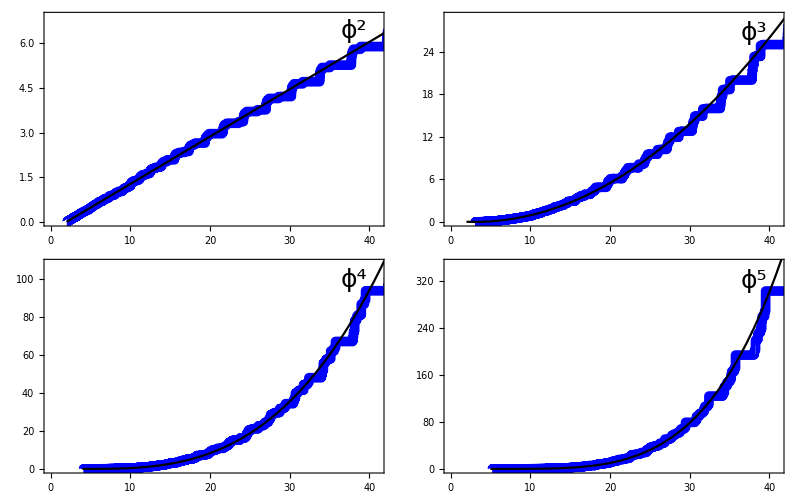
-Graphics-Free Theory Spectral Densitiesϕ^𝓃 Integrated Spectral Densityμ / 𝓂

```mathematica
grid=Labeled[GraphicsGrid[{{plot2ZoomOut,plot3ZoomOut},{plot4ZoomOut,plot5ZoomOut}},ImageSize->800,Spacings->{0,0}],{Style["Free Theory Spectral Densities",FontFamily->"Times",FontSize->25],Style["ϕ^𝓃 Integrated Spectral Density",FontFamily->"Times",FontSize->25],Style["μ / 𝓂",FontFamily->"Times",FontSize->25]},{Top,Left,Bottom},RotateLabel->True,LabelStyle->{FontFamily->"Times",20}]
```

```mathematica
Specϕ2D16//Length
Specϕ3D16//Length
Specϕ4D16//Length
Specϕ5D16//Length
```

455

6045

13520

8060

```mathematica
(* Save *)
SetDirectory[NotebookDirectory[]];
filename="FreeSpectralDensitiesD16IR05";
DeleteFile[filename];
Save[filename,{Specϕ2D16,Specϕ3D16,Specϕ4D16,Specϕ5D16}];
```

DeleteFile::fdnfnd: Directory or file FreeSpectralDensitiesD16IR05 not found.

```mathematica
dir=NotebookDirectory[];
SetDirectory[dir];
Export["./FreeSpectralDensities.pdf",grid]
```

./FreeSpectralDensities.pdf

### Scratch

```mathematica
DMAX=16;
npart=3;
```

```mathematica
(* Load data *)
dir="/Users/khandker/Dropbox/Higher D Basis/Dmax"<>ToString[DMAX]<>" Data/";
Get[dir<>"Basis"<>ToString[npart]<>"_Dmax"<>ToString[DMAX]];
Get[dir<>"Bas"<>ToString[npart]<>"Mass"];
```

```mathematica
dmax=16;
kmax=50;
m=1.;
ΛIR=.5;
Λ=ΛIR*√((1-ratioWidth^kmax)/(ratioWidth^(kmax-1)(1-ratioWidth)))
```

20.8404

```mathematica
t1=AbsoluteTime[];

kinetic=kineticFunc[npart,dmax,kmax];
mass=massFunc[npart,dmax,kmax];
ϕnOverlaps=ϕnOverlapFunc[npart,dmax,kmax];

{vals,vecs}=eigensys[Λ^2*kinetic+m^2*mass];
ϕnIntegratedSpec=Thread[{√vals,Λ^(npart-1)*Accumulate[(vecs.ϕnOverlaps)^2]}];

t2=AbsoluteTime[];
Print["Elapsed Time: "<>ToString[(t2-t1)/60//N]]
```

Elapsed Time: 0.253544

```mathematica
Specϕ2D16=ϕnIntegratedSpec;
```

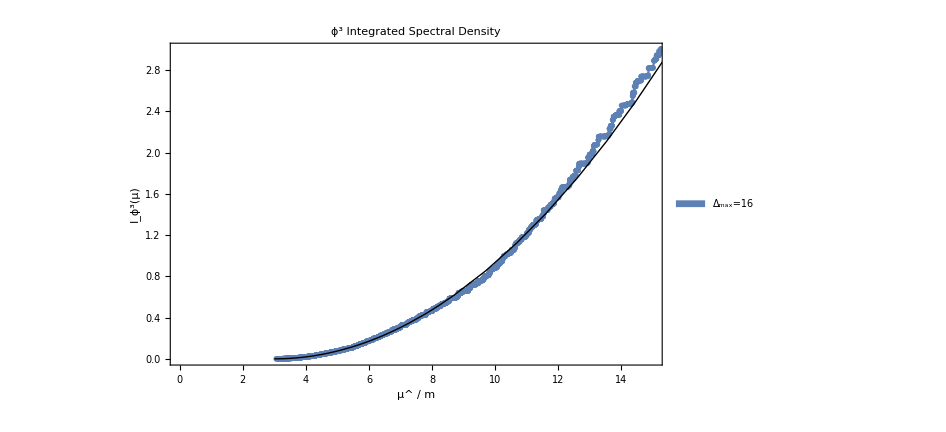

```mathematica
plot=ListPlot[{Specϕ2D16},Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->14,LabelStyle->Black,ImageSize->700,PlotRange->{{0,15},{0,3}},Joined->True,PlotMarkers->{Style["●"],2},FrameLabel->{Style["μ^ / m",FontFamily->"Times",FontSize->14,FontColor->Black],Style["I_(ϕ^3)(μ)",FontFamily->"Times",FontSize->14,FontColor->Black]},PlotLabel->Style["ϕ^3 Integrated Spectral Density",FontFamily->"Times",FontSize->16,FontColor->Black],PlotLegends->Placed[SwatchLegend[{"Δ_max=16","",""},LabelStyle->{FontFamily->"Times",14},LegendLayout->{"Row",5}],{.9,.15}]];
thy3=Plot[3/(4π)^2(x-3m)^2,{x,3m,50},PlotStyle->{Black,Thick}];
Show[plot,thy3]
```